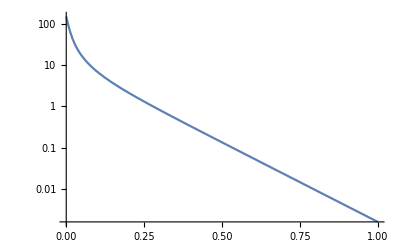

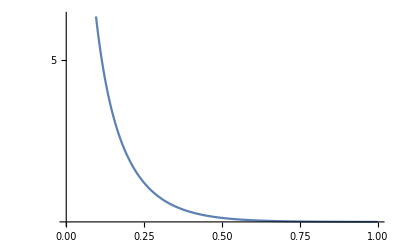

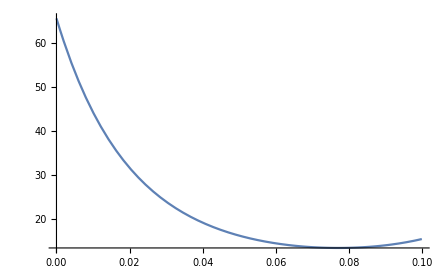

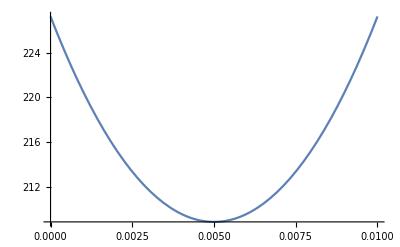

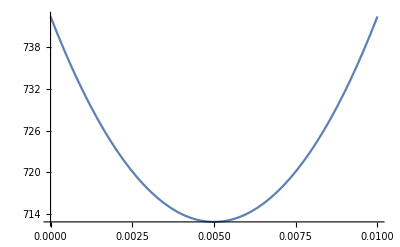

-Graphics3D-

-Graphics3D-

$Aborted

$Aborted

$Aborted

```mathematica
LogPlot[4*Sum[(-1)^(n+m+1)*Exp[-2*π*z*√((2*n+1)^2+(2*m+1)^2)]/(√((2*n+1)^2+(2*m+1)^2))*Cos[2*π*((2*n+1)*0+(2*m+1)*0-(n+m+1)/2)],{n,-11,10},{m,-11,10}],{z,0.00000001,1},AxesLabel->{"z/L","u/e/(4  πϵL)"}]
Plot[Sum[Exp[-2*π*z*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-((-1)^m+(-1)^n)*Exp[-2*π*0.1*√(n^2+m^2)]),{n,-11,-1},{m,-11,-1}]+Sum[Exp[-2*π*0.1*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-((-1)^m+(-1)^n)*Exp[-2*π*0.1*√(n^2+m^2)]),{n,-11,-1},{m,1,10}]+Sum[Exp[-2*π*0.1*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-((-1)^m+(-1)^n)*Exp[-2*π*0.1*√(n^2+m^2)]),{n,1,10},{m,-11,-1}]+Sum[Exp[-2*π*0.1*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-((-1)^m+(-1)^n)*Exp[-2*π*0.1*√(n^2+m^2)]),{n,1,10},{m,1,10}],{z,0.00000001,1},AxesLabel->{"z/L","u/e/(4  πϵL)"}]
Plot[Sum[Exp[-2*π*z*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m)))-(((-1)^m+(-1)^n)*Exp[2*π*(z-0.1)*√(n^2+m^2)])/(√(n^2+m^2)),{n,-11,-1},{m,-11,-1}]+Sum[Exp[-2*π*z*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m)))-(((-1)^m+(-1)^n)*Exp[2*π*(z-0.1)*√(n^2+m^2)])/(√(n^2+m^2)),{n,-11,-1},{m,1,10}]+Sum[Exp[-2*π*z*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m)))-(((-1)^m+(-1)^n)*Exp[2*π*(z-0.1)*√(n^2+m^2)])/(√(n^2+m^2)),{n,1,10},{m,-11,-1}]+Sum[Exp[-2*π*z*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m)))-(((-1)^m+(-1)^n)*Exp[2*π*(z-0.1)*√(n^2+m^2)])/(√(n^2+m^2)),{n,1,10},{m,1,10}],{z,0.00000001,0.1-0.00000001},AxesLabel->{"z/L","u/e/(4  πϵL)"}]
Plot[4*Sum[(-1)^(n+m+1)*(Exp[-2*π*z*√((2*n+1)^2+(2*m+1)^2)]+Exp[-2*π*(0.01-z)*√((2*n+1)^2+(2*m+1)^2)])/(√((2*n+1)^2+(2*m+1)^2))*Cos[2*π*((2*n+1)*0+(2*m+1)*0-(n+m+1)/2)],{n,-11,10},{m,-11,10}],{z,0.00000001,0.01-0.00000001},AxesLabel->{"z/L","u/e/(4  πϵL)"}]
Plot[4*Sum[(-1)^(n+m+1)*(Exp[-2*π*z*√((2*n+1)^2+(2*m+1)^2)]+Exp[-2*π*(0.01-z)*√((2*n+1)^2+(2*m+1)^2)])/((1-Exp[-2*π*0.01*√((2*n+1)^2+(2*m+1)^2)])*√((2*n+1)^2+(2*m+1)^2))*Cos[2*π*((2*n+1)*0+(2*m+1)*0-(n+m+1)/2)],{n,-11,10},{m,-11,10}],{z,0.00000001,0.01-0.00000001},AxesLabel->{"z/L","u/e/(4  πϵL)"}]
one=Show[Plot3D[4*Sum[(-1)^(n+m+1)*Exp[-2*π*0.1*√((2*n+1)^2+(2*m+1)^2)]/(√((2*n+1)^2+(2*m+1)^2))*Cos[2*π*((2*n+1)*x+(2*m+1)*y-(n+m+1)/2)],{n,-11,10},{m,-11,10}],{x,-2,2},{y,-2,2},Mesh->None,ColorFunction->"Rainbow",PlotLegends->Automatic]]
two=Show[Plot3D[Sum[Exp[-2*π*0.1*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-((-1)^m+(-1)^n)*Exp[-2*π*0.1*√(n^2+m^2)])*Cos[2*π*(n*x+m*y)],{n,-11,-1},{m,-11,-1}]+Sum[Exp[-2*π*0.1*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-((-1)^m+(-1)^n)*Exp[-2*π*0.1*√(n^2+m^2)])*Cos[2*π*(n*x+m*y)],{n,-11,-1},{m,1,10}]+Sum[Exp[-2*π*0.1*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-((-1)^m+(-1)^n)*Exp[-2*π*0.1*√(n^2+m^2)])*Cos[2*π*(n*x+m*y)],{n,1,10},{m,-11,-1}]+Sum[Exp[-2*π*0.1*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-((-1)^m+(-1)^n)*Exp[-2*π*0.1*√(n^2+m^2)])*Cos[2*π*(n*x+m*y)],{n,1,10},{m,1,10}],{x,-2,2},{y,-2,2},Mesh->None,ColorFunction->"Rainbow",PlotLegends->Automatic]]
three=Show[Plot3D[Sum[Exp[-2*π*0.1*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-(1+(-1)^(m+n))*Exp[-2*π*0.1*√(n^2+m^2)])*Cos[2*π*(n*x+m*y)],{n,-11,-1},{m,-11,-1}]+Sum[Exp[-2*π*0.1*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-(1+(-1)^(m+n))*Exp[-2*π*0.1*√(n^2+m^2)])*Cos[2*π*(n*x+m*y)],{n,-11,-1},{m,1,10}]+Sum[Exp[-2*π*0.1*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-(1+(-1)^(m+n))*Exp[-2*π*0.1*√(n^2+m^2)])*Cos[2*π*(n*x+m*y)],{n,1,10},{m,-11,-1}]+Sum[Exp[-2*π*0.1*√(n^2+m^2)]/(√(n^2+m^2))*((1+(-1)^(n+m))-(1+(-1)^(m+n))*Exp[-2*π*0.1*√(n^2+m^2)])*Cos[2*π*(n*x+m*y)],{n,1,10},{m,1,10}],{x,-2,2},{y,-2,2},Mesh->None,ColorFunction->"Rainbow",PlotLegends->Automatic]]
four=Show[Plot3D[4*Sum[(Exp[-2*π*0.4*√((2*n+1)^2+(2*m+1)^2)]+Exp[-2*π*0.6*√((2*n+1)^2+(2*m+1)^2)])/(√((2*n+1)^2+(2*m+1)^2))*Cos[2*π*((2*n+1)*x+(2*m+1)*y)],{n,-11,10},{m,-11,10}],{x,-2,2},{y,-2,2},Mesh->None,ColorFunction->"Rainbow",PlotLegends->Automatic]]
five=Show[Plot3D[4*Sum[(Exp[-2*π*0.4*√((2*n+1)^2+(2*m+1)^2)]+Exp[-2*π*0.6*√((2*n+1)^2+(2*m+1)^2)])/((1-Exp[-2*π*√((2*n+1)^2+(2*m+1)^2)])*√((2*n+1)^2+(2*m+1)^2))*Cos[2*π*((2*n+1)*x+(2*m+1)*y)],{n,-11,10},{m,-11,10}],{x,-2,2},{y,-2,2},Mesh->None,ColorFunction->"Rainbow",PlotLegends->Automatic]]
```